```mathematica
SetDirectory[NotebookDirectory[]];
<<FourPointSpectrum`
?intervals
?image
?points
?numerical
```

Generates the set of possible eigenvalues E1, E2 for self-adjoint operators with diagonal elements beta^k, 1-beta^k, assuming there are exactly 4 eigenvalues: 0, 1, E1, E2.

- Generate an image:
b = 95/100;
im = image[b] // AbsoluteTiming;
Export[" image.png ", im[[2, 1]], ImageSize -> 2000]

- Export a movie. Saving avi takes longer than generating the data:
B = 0.80;
animate=Monitor[Table[image[b],
{b,0.01,B,0.002}],Row[{ProgressIndicator[b,{1/100,B}],"b=",N[b]}]] // AbsoluteTiming;
animate[[1]]
Export["~/movie.avi",animate[[2,All,1]],ImageSize->800]

- Manipulate beta almost in real time:
B=0.8
Manipulate[image[b],{b,0.01,0.8}]

- Use points[beta] instead of image[beta] for the endpoints of the intervals.

- Use intervals[beta] to get the intervals as a array.

- numerical[True/False] force numerical computations/try rationals

Generate intervals for a given beta.

Plot intervals.

Plot the endpoints of the intervals.

Numerical[True/False] force numerical computations, or try rationals.

```mathematica
Manipulate[points[b],{b,0.01,0.8}]
```

```mathematica
numerical[False]
```

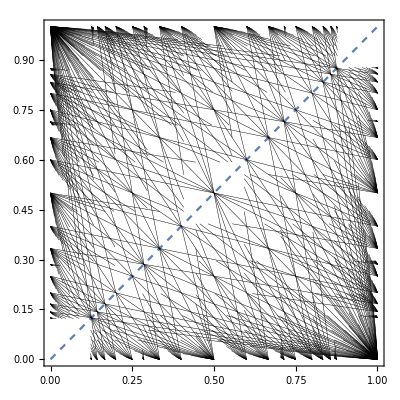
-Graphics-0.666667

179/1458

{{13/7290,179/1458},{13/6561,179/1458},{13/5832,179/1458},{13/5103,179/1458},{13/4374,179/1458},{13/3645,179/1458},{13/2916,179/1458},{205/5832,179/1458},{13/2187,179/1458},{205/4374,179/1458},{64/729,179/1458},{13/1458,179/1458},{205/2916,179/1458},{13/729,179/1458}}

```mathematica
B=2/3;
image[B]
(* only upper half *)
ints=intervals[B][[All,2]]//Select[#,#[[1]]<=#[[2]]&]&;
(* minimal y *)
miny = Min[ints[[All,2]]]
(* all points with minimal y *)
Sort[ints,#1[[2]]<#2[[2]]&]//Select[#,#[[2]]==miny&]&
```